```mathematica
b =9;
p[v_]=(1/b)*E^(-(1-v)/b);
```

```mathematica
p[1]
```

85/3

```mathematica
85/3//N
```

28.3333

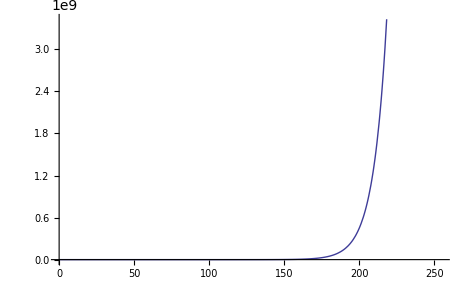

```mathematica
Plot[p[v],{v,0,255}]
```

```mathematica
Integrate[p[v],{v,0,1}]
```

1-1/ⅇ^(1/9)

```mathematica
a = {5.210064241264206e-14,5.822346138982942e-14,6.506582835129226e-14,7.271230390605362e-14,8.125738614717446e-14,9.080667849560482e-14,1.0147819478794686e-13,1.1340381773707643e-13,1.2673092878943105e-13,1.4162422952153217e-13,1.582677770865164e-13,1.7686725886246515e-13,1.9765253441472928e-13,2.2088047619605425e-13,2.468381440684981e-13,2.758463328880761e-13,3.082635370629472e-13,3.4449038086206426e-13,3.8497456966045023e-13,4.302164227092956e-13,4.807750560369964e-13,5.372752932584476e-13,6.004153853080177e-13,6.709756432308134e-13,7.498280786441423e-13,8.379471756296013e-13,9.364219546287245e-13,1.0464693892364647e-12,1.1694495170726992e-12,1.3068821313191124e-12,1.4604657560231202e-12,1.632098320888698e-12,1.823901141561202e-12,2.0382442760774355e-12,2.2777772418854923e-12,2.545459423004367e-12,2.8445993647671226e-12,3.178895111169605e-12,3.55247568911325e-12,3.969962254436453e-12,4.436507936682368e-12,4.957890184092438e-12,5.540535231702867e-12,6.1916521827155415e-12,6.9193110356471854e-12,7.732457703507185e-12,8.641227794794604e-12,9.656725091284042e-12,1.0791562684366808e-11,1.2059937087214808e-11,1.3477177731836814e-11,1.5060971177197906e-11,1.683135742545268e-11,1.8809276078424153e-11,2.1019637889540013e-11,2.348975936228077e-11,2.6251436300164724e-11,2.9336244707693807e-11,3.278357692652276e-11,3.6639486161603856e-11,4.094468310416144e-11,4.575582278215876e-11,5.1132363114701306e-11,5.714074946017736e-11,6.386461315072678e-11,7.136817964279965e-11,7.975355828126363e-11,8.912437880836776e-11,9.96219397909658e-11,1.1132467840785753e-10,1.2440271196873593e-10,1.3901766385466348e-10,1.5535015127593251e-10,1.7360201740918714e-10,1.93998825853223e-10,2.1686193819644752e-10,2.423344693530261e-10,2.7080050864962344e-10,3.0261185037512617e-10,3.381616313556392e-10,3.778891894909599e-10,4.222854932617311e-10,4.718992093072242e-10,5.27343483059207e-10,5.893035162295915e-10,6.58545034797376e-10,7.359237521455176e-10,8.223959442968527e-10,9.190302679418801e-10,1.0270209673101727e-09,1.1478909827552283e-09,1.2825666958697987e-09,1.4332798577019223e-09,1.6017046899596987e-09,1.7899226516574166e-09,2.0002598129343385e-09,2.235315601526332e-09,2.49799492749604e-09,2.7915440832314543e-09,3.1195908623788487e-09,3.486189393515413e-09,3.895870242633281e-09,4.353696403620856e-09,4.865325868693363e-09,5.43708155204208e-09,6.076044119037202e-09,6.790011267566991e-09,7.58796060336206e-09,8.479684202002942e-09,9.476202327531242e-09,1.0589830335156013e-08,1.1834330869161709e-08,1.3225083946972528e-08,1.4779251540983724e-08,1.6516091949268348e-08,1.8457044224887812e-08,2.0626095404410513e-08,2.3050042081227013e-08,2.575885919358067e-08,2.878601397037014e-08,3.216891715746539e-08,3.594937597675203e-08,4.017410734615387e-08,4.4895329066927344e-08,5.017138436764997e-08,5.6067475504854206e-08,6.265647119995199e-08,7.001979953308183e-08,7.824845935476164e-08,8.744414314880675e-08,9.772049566051134e-08,1.0920451554945434e-07,1.2203812658940637e-07,1.3637993183930573e-07,1.5240717268625065e-07,1.7031791988884556e-07,1.9033352149377002e-07,2.1270133793636911e-07,2.3769779936306725e-07,2.656318216584733e-07,2.968486242316984e-07,3.3173399638198344e-07,3.7071906497693754e-07,4.142856225315246e-07,4.629720813570575e-07,5.173801274853991e-07,5.781821565268081e-07,6.461295833983533e-07,7.220621285997241e-07,8.06918195800203e-07,9.017464689953572e-07,1.007718872546744e-06,1.126145054275891e-06,1.2584885705964812e-06,1.4063849737091142e-06,1.5716620243858072e-06,1.7563622801424356e-06,1.9627683379519637e-06,2.1934310434579497e-06,2.451201015308487e-06,2.7392638742005073e-06,3.061179612008636e-06,3.420926587537327e-06,3.822950692612852e-06,4.2722202961286316e-06,4.774287645063613e-06,5.3353574812911295e-06,5.962363722171253e-06,6.663055152574969e-06,7.446091187355109e-06,8.321148887733933e-06,9.299042554156674e-06,1.039185737358598e-05,1.1613098772901927e-05,1.2977859324174494e-05,1.4503005264488244e-05,1.6207384935403098e-05,1.8112061718026494e-05,2.0240574342397974e-05,2.2619227788190896e-05,2.5277418371793015e-05,2.824799703731845e-05,3.156767534124089e-05,3.527747914796285e-05,3.9423255643265805e-05,4.405623993150866e-05,4.923368821880167e-05,5.5019585407276355e-05,6.148543584517673e-05,6.871114700516333e-05,7.678601701166925e-05,8.580983822155134e-05,9.589413049651186e-05,0.0001071635194085465,0.00011975727641081333,0.00013383104000794832,0.0001495587391967113,0.00016713474294758989,0.00018677626229147518,0.0002087260346973292,0.000233255323915415,0.0002606672723593101,0.00029130064745673165,0.0003255340282680224,0.0003637904841121429,0.0004065428030204274,0.00045431933463336855,0.0005077105197491789,0.0005673761872188235,0.0006340537083653627,0.0007085671097030587,0.0007918372565747497,0.0008848932335608,0.000988885062303119,0.0011050979139159943,0.0012349679916262514,0.0013801002799264518,0.001542288379592067,0.0017235366736913975,0.0019260850985243331,0.0021524368256187663,0.00240538919688945,0.0026880682952679195,0.0030039675780406073,0.0033569910503409637,0.003751501512350077,0.004192374476448733,0.004685058420738146,0.005235642123344517,0.005850929909945637,0.006538525744236362,0.0073069272006437425,0.008165630480627985,0.00912524777040156,0.010197638390417912,0.0113960553574261,0.012735309170361534,0.014231950844202132,0.01590447645379274,0.017773555715469354,0.019862287431383005,0.02219648495340235,0.02480499519446897,0.027720055129869355,0.030977690194204714,0.034618159497601594,0.03868645336331702,0.043232849335499555,0.04831353352846475,0.05399129499635891,0.06033630170449821,0.06742696769213893,0.07535092214340681,0.08420609234254062,0.09410191389702732,0.10516068318503298}
```

{-14+5.21006 e,-14+5.82235 e,-14+6.50658 e,-14+7.27123 e,-14+8.12574 e,-14+9.08067 e,-13+1.01478 e,-13+1.13404 e,-13+1.26731 e,-13+1.41624 e,-13+1.58268 e,-13+1.76867 e,-13+1.97653 e,-13+2.2088 e,-13+2.46838 e,-13+2.75846 e,-13+3.08264 e,-13+3.4449 e,-13+3.84975 e,-13+4.30216 e,-13+4.80775 e,-13+5.37275 e,-13+6.00415 e,-13+6.70976 e,-13+7.49828 e,-13+8.37947 e,-13+9.36422 e,-12+1.04647 e,-12+1.16945 e,-12+1.30688 e,-12+1.46047 e,-12+1.6321 e,-12+1.8239 e,-12+2.03824 e,-12+2.27778 e,-12+2.54546 e,-12+2.8446 e,-12+3.1789 e,-12+3.55248 e,-12+3.96996 e,-12+4.43651 e,-12+4.95789 e,-12+5.54054 e,-12+6.19165 e,-12+6.91931 e,-12+7.73246 e,-12+8.64123 e,-12+9.65673 e,-11+1.07916 e,-11+1.20599 e,-11+1.34772 e,-11+1.5061 e,-11+1.68314 e,-11+1.88093 e,-11+2.10196 e,-11+2.34898 e,-11+2.62514 e,-11+2.93362 e,-11+3.27836 e,-11+3.66395 e,-11+4.09447 e,-11+4.57558 e,-11+5.11324 e,-11+5.71407 e,-11+6.38646 e,-11+7.13682 e,-11+7.97536 e,-11+8.91244 e,-11+9.96219 e,-10+1.11325 e,-10+1.24403 e,-10+1.39018 e,-10+1.5535 e,-10+1.73602 e,-10+1.93999 e,-10+2.16862 e,-10+2.42334 e,-10+2.70801 e,-10+3.02612 e,-10+3.38162 e,-10+3.77889 e,-10+4.22285 e,-10+4.71899 e,-10+5.27343 e,-10+5.89304 e,-10+6.58545 e,-10+7.35924 e,-10+8.22396 e,-10+9.1903 e,-9+1.02702 e,-9+1.14789 e,-9+1.28257 e,-9+1.43328 e,-9+1.6017 e,-9+1.78992 e,-9+2.00026 e,-9+2.23532 e,-9+2.49799 e,-9+2.79154 e,-9+3.11959 e,-9+3.48619 e,-9+3.89587 e,-9+4.3537 e,-9+4.86533 e,-9+5.43708 e,-9+6.07604 e,-9+6.79001 e,-9+7.58796 e,-9+8.47968 e,-9+9.4762 e,-8+1.05898 e,-8+1.18343 e,-8+1.32251 e,-8+1.47793 e,-8+1.65161 e,-8+1.8457 e,-8+2.06261 e,-8+2.305 e,-8+2.57589 e,-8+2.8786 e,-8+3.21689 e,-8+3.59494 e,-8+4.01741 e,-8+4.48953 e,-8+5.01714 e,-8+5.60675 e,-8+6.26565 e,-8+7.00198 e,-8+7.82485 e,-8+8.74441 e,-8+9.77205 e,-7+1.09205 e,-7+1.22038 e,-7+1.3638 e,-7+1.52407 e,-7+1.70318 e,-7+1.90334 e,-7+2.12701 e,-7+2.37698 e,-7+2.65632 e,-7+2.96849 e,-7+3.31734 e,-7+3.70719 e,-7+4.14286 e,-7+4.62972 e,-7+5.1738 e,-7+5.78182 e,-7+6.4613 e,-7+7.22062 e,-7+8.06918 e,-7+9.01746 e,-6+1.00772 e,-6+1.12615 e,-6+1.25849 e,-6+1.40638 e,-6+1.57166 e,-6+1.75636 e,-6+1.96277 e,-6+2.19343 e,-6+2.4512 e,-6+2.73926 e,-6+3.06118 e,-6+3.42093 e,-6+3.82295 e,-6+4.27222 e,-6+4.77429 e,-6+5.33536 e,-6+5.96236 e,-6+6.66306 e,-6+7.44609 e,-6+8.32115 e,-6+9.29904 e,-5+1.03919 e,-5+1.16131 e,-5+1.29779 e,-5+1.4503 e,-5+1.62074 e,-5+1.81121 e,-5+2.02406 e,-5+2.26192 e,-5+2.52774 e,-5+2.8248 e,-5+3.15677 e,-5+3.52775 e,-5+3.94233 e,-5+4.40562 e,-5+4.92337 e,-5+5.50196 e,-5+6.14854 e,-5+6.87111 e,-5+7.6786 e,-5+8.58098 e,-5+9.58941 e,0.000107164,0.000119757,0.000133831,0.000149559,0.000167135,0.000186776,0.000208726,0.000233255,0.000260667,0.000291301,0.000325534,0.00036379,0.000406543,0.000454319,0.000507711,0.000567376,0.000634054,0.000708567,0.000791837,0.000884893,0.000988885,0.0011051,0.00123497,0.0013801,0.00154229,0.00172354,0.00192609,0.00215244,0.00240539,0.00268807,0.00300397,0.00335699,0.0037515,0.00419237,0.00468506,0.00523564,0.00585093,0.00653853,0.00730693,0.00816563,0.00912525,0.0101976,0.0113961,0.0127353,0.014232,0.0159045,0.0177736,0.0198623,0.0221965,0.024805,0.0277201,0.0309777,0.0346182,0.0386865,0.0432328,0.0483135,0.0539913,0.0603363,0.067427,0.0753509,0.0842061,0.0941019,0.105161}

```mathematica
DiscretePlot[a,{1,256}]
```

Internal`LocalizedBlock::novar: -- Message text not found -- (1)

```mathematica
DiscretePlot[a,{n,256}]
```